```mathematica
(*S.aureus growth with Sodium benzoate*)
data1={{8.0,36.0},{16.0,35.67},{32.0,32.13},{64.0,2.8}};
model1=LinearModelFit[data1,x,x];
r21=model1["RSquared"];
(*S.aureus growth with Sodium nitrite*)
data2={{0.0,1.54},{2.0,1.2},{4.0,0.99}};
model2=LinearModelFit[data2,x,x];
r22=model2["RSquared"];
(*S.aureus growth with Vitamin E*)
data3={{50.0,3.25},{100.0,3.0},{200.0,2.85},{400.0,2.1}};
model3=LinearModelFit[data3,x,x];
r23=model3["RSquared"];
```

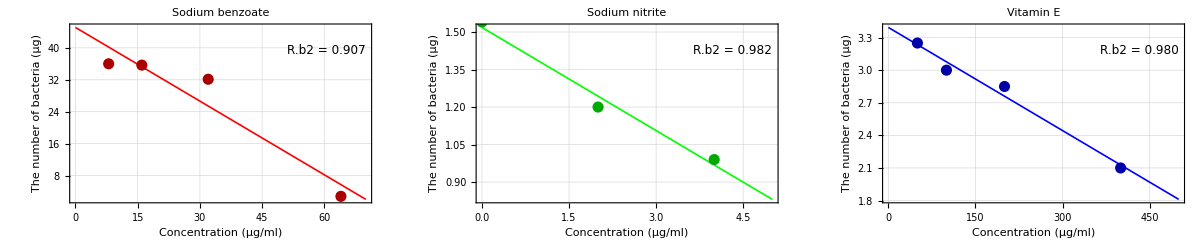
STAPHYLOCOCCUS AUREUS
-Graphics-

```mathematica
(*Create three subplots*)plot1=Plot[model1[x],{x,0,70},FrameLabel->{"Concentration (μg/ml)","The number of bacteria (μg)"},PlotStyle->{Red,Thickness[0.003]},Epilog->{{Darker[Red],PointSize[0.02],Point[data1]},{Darker[Red],PointSize[0.005],Point[data1]},Text[Style["R.b2 = "<>ToString[NumberForm[r21,{4,3}]],12],Scaled[{0.85,0.85}]]},PlotLabel->Style["Sodium benzoate",12],ImageSize->400,PlotRange->All,Frame->True,FrameStyle->GrayLevel[0.3],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],LabelStyle->Directive[Black,12]];

plot2=Plot[model2[x],{x,0,5},FrameLabel->{"Concentration (μg/ml)","The number of bacteria (μg)"},PlotStyle->{Green,Thickness[0.003]},Epilog->{{Darker[Green],PointSize[0.02],Point[data2]},{Darker[Green],PointSize[0.005],Point[data2]},Text[Style["R.b2 = "<>ToString[NumberForm[r22,{4,3}]],12],Scaled[{0.85,0.85}]]},PlotLabel->Style["Sodium nitrite",12],ImageSize->400,PlotRange->All,Frame->True,FrameStyle->GrayLevel[0.3],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],LabelStyle->Directive[Black,12]];

plot3=Plot[model3[x],{x,0,500},FrameLabel->{"Concentration (μg/ml)","The number of bacteria (μg)"},PlotStyle->{Blue,Thickness[0.003]},Epilog->{{Darker[Blue],PointSize[0.02],Point[data3]},{Darker[Blue],PointSize[0.005],Point[data3]},Text[Style["R.b2 = "<>ToString[NumberForm[r23,{4,3}]],12],Scaled[{0.85,0.85}]]},PlotLabel->Style["Vitamin E",12],ImageSize->400,PlotRange->All,Frame->True,FrameStyle->GrayLevel[0.3],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],LabelStyle->Directive[Black,12]];

(*Create main title*)
title=Style["STAPHYLOCOCCUS AUREUS",Bold,16];  (*Bold,font size 16*)

(*Combine title and plots using Column*)
Column[{Text[title],(*Add title*)GraphicsRow[{plot1,plot2,plot3},ImageSize->Full,Spacings->20]},Alignment->Center  (*Center alignment*)]
```

```mathematica
(*Salmonella-Sodium benzoate*)
data4={{0.0,3.39},{100.0,3.0},{200.0,2.71},{300.0,2.47},{400.0,2.32}};
model4=LinearModelFit[data4,x,x];
r24=model4["RSquared"];
(*Salmonella-Sodium nitrite*)
data5={{25.0,4.03},{50.0,3.2},{75.0,2.76},{100.0,1.27},{200.0,0.72},{300.0,0.54}};
model5=LinearModelFit[data5,x,x];
r25=model5["RSquared"];
(*Salmonella-Vitamin E*)
data6={{1019.0,14.4},{1024.0,13.9},{1069.0,10.1}};
model6=LinearModelFit[data6,x,x];
r26=model6["RSquared"];
```

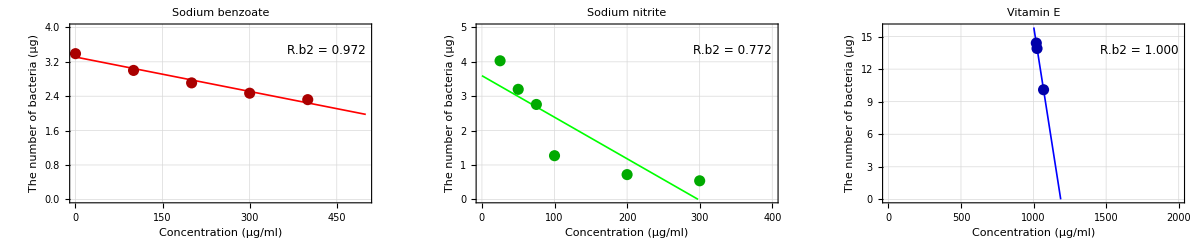
SALMONELLA
-Graphics-

```mathematica
(*Create three subplots*)plot4=Plot[model4[x],{x,0,500},FrameLabel->{"Concentration (μg/ml)","The number of bacteria (μg)"},PlotStyle->{Red,Thickness[0.003]},Epilog->{{Darker[Red],PointSize[0.02],Point[data4]},{Darker[Red],PointSize[0.005],Point[data4]},Text[Style["R.b2 = "<>ToString[NumberForm[r24,{4,3}]],12],Scaled[{0.85,0.85}]]},PlotLabel->Style["Sodium benzoate",12],ImageSize->400,PlotRange->{{0,500},{0,4}},(*Set minimum y-axis value to 0*)Frame->True,FrameStyle->GrayLevel[0.3],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],LabelStyle->Directive[Black,12]];

plot5=Plot[model5[x],{x,0,400},FrameLabel->{"Concentration (μg/ml)","The number of bacteria (μg)"},PlotStyle->{Green,Thickness[0.003]},Epilog->{{Darker[Green],PointSize[0.02],Point[data5]},{Darker[Green],PointSize[0.005],Point[data5]},Text[Style["R.b2 = "<>ToString[NumberForm[r25,{4,3}]],12],Scaled[{0.85,0.85}]]},PlotLabel->Style["Sodium nitrite",12],ImageSize->400,PlotRange->{{0,400},{0,5}},(*Set minimum y-axis value to 0*)Frame->True,FrameStyle->GrayLevel[0.3],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],LabelStyle->Directive[Black,12]];

plot6=Plot[model6[x],{x,0,2000},FrameLabel->{"Concentration (μg/ml)","The number of bacteria (μg)"},PlotStyle->{Blue,Thickness[0.003]},Epilog->{{Darker[Blue],PointSize[0.02],Point[data6]},{Darker[Blue],PointSize[0.005],Point[data6]},Text[Style["R.b2 = "<>ToString[NumberForm[r26,{4,3}]],12],Scaled[{0.85,0.85}]]},PlotLabel->Style["Vitamin E",12],ImageSize->400,PlotRange->{{0,2000},{0,Max[data6[[All,2]]]*1.1}},(*Ensure all points are visible with some padding*)Frame->True,FrameStyle->GrayLevel[0.3],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],LabelStyle->Directive[Black,12]];

(*Create main title*)
title=Style["SALMONELLA",Bold,16];  (*Bold,font size 16*)

(*Combine title and plots using Column*)
Column[{Text[title],(*Add title*)GraphicsRow[{plot4,plot5,plot6},ImageSize->Full,Spacings->20]},Alignment->Center  (*Center alignment*)]
```

```mathematica
(*Bacillus subtilis-Sodium benzoate*)
data7={{0.0,3.12},{100.0,2.9},{200.0,2.75},{300.0,2.66},{400.0,2.49}};
model7=LinearModelFit[data7,{x},x];
r27=model7["RSquared"];
(*Bacillus subtilis-Sodium bisulfite*)
data8={{0.781,15.0},{1.563,10.7},{3.125,8.76},{6.25,7.53}};
model8=LinearModelFit[data8,{x},x];
r28=model8["RSquared"];
```

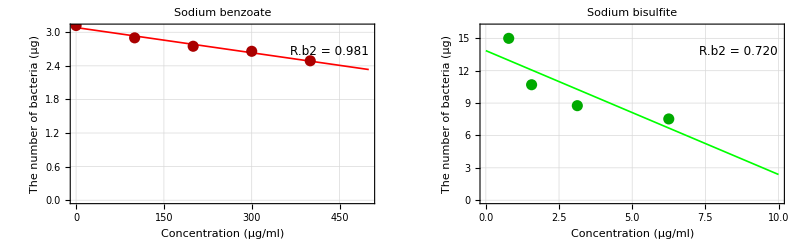
BACILLUS SUBTILIS
-Graphics-

```mathematica
(*Create the first two subplots*)plot7=Plot[model7[x],{x,0,500},FrameLabel->{"Concentration (μg/ml)","The number of bacteria (μg)"},PlotStyle->{Red,Thickness[0.003]},Epilog->{{Darker[Red],PointSize[0.02],Point[data7]},{Darker[Red],PointSize[0.005],Point[data7]},Text[Style["R.b2 = "<>ToString[NumberForm[r27,{4,3}]],12],Scaled[{0.85,0.85}]]},PlotLabel->Style["Sodium benzoate",12],ImageSize->400,PlotRange->{{0,500},{0,Automatic}},(*Set minimum y-axis value to 0*)Frame->True,FrameStyle->GrayLevel[0.3],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],LabelStyle->Directive[Black,12]];

plot8=Plot[model8[x],{x,0,10},FrameLabel->{"Concentration (μg/ml)","The number of bacteria (μg)"},PlotStyle->{Green,Thickness[0.003]},Epilog->{{Darker[Green],PointSize[0.02],Point[data8]},{Darker[Green],PointSize[0.005],Point[data8]},Text[Style["R.b2 = "<>ToString[NumberForm[r28,{4,3}]],12],Scaled[{0.85,0.85}]]},PlotLabel->Style["Sodium bisulfite",12],ImageSize->400,PlotRange->{{0,10},{0,16}},(*Set minimum y-axis value to 0*)Frame->True,FrameStyle->GrayLevel[0.3],GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],LabelStyle->Directive[Black,12]];

(*Create an empty subplot with the same style and size as others*)
emptyPlot=Plot[0,{x,0,1},ImageSize->400,PlotStyle->None,(*Hide line*)Axes->False,(*Hide axes*)Frame->False      (*Hide frame*)];

(*Create main title*)
title=Style["BACILLUS SUBTILIS",Bold,16];  (*Bold,font size 16*)

(*Use Column to combine title and plots*)
Column[{Text[title],(*Add title*)GraphicsRow[{plot7,plot8,emptyPlot},ImageSize->Full,Spacings->20]},Alignment->Center  (*Center alignment*)]
```

```mathematica
(* linear optimization *)
res=LinearOptimization[model1[Subscript[x, 1]]+model2[Subscript[x, 2]]+model3[Subscript[x, 3]]+model4[Subscript[x, 1]]+model5[Subscript[x, 2]]+model6[Subscript[x, 3]]+model7[Subscript[x, 1]]+model8[Subscript[x, 4]],{Subscript[x, 2]+Subscript[x, 3]<230,Subscript[x, 1]+Subscript[x, 3]<700,Subscript[x, 1]+Subscript[x, 2]<1030,Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 3]<1230,Subscript[x, 2]+Subscript[x, 3]<230,Subscript[x, 1]+Subscript[x, 4]<1500,Subscript[x, 1]>=0,Subscript[x, 2]>=0,Subscript[x, 3]>=0,Subscript[x, 4]>=0},{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]}]
```

{x_1→0.,x_2→230.,x_3→0.,x_4→1500.}